```mathematica
g[s1_,s2_,t_]:=ⅇ^(mx0(ⅇ^(ktl (-1+s2) t) s1-1)+my0(s2-1))
```

```mathematica
Simplify[D[g[s1,s2,t], t]==ktl(s1 s2-s1)D[g[s1,s2,t], s1]]
```

True

```mathematica
mx0=2;my0=0;ktl=20;kin=1;
```

```mathematica
nmax=50;
```

```mathematica
Clear[mean,stddev]
```

```mathematica
mean[t_]:=D[g[1,s,t],{s,1}]/.s->1
```

```mathematica
stddev[t_]:=√(D[Log[g[1,ⅇ^τ,t]],{τ,2}]/.τ->0)
```

```mathematica
origin=-1;
```

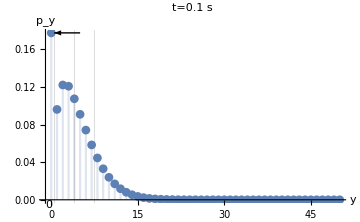
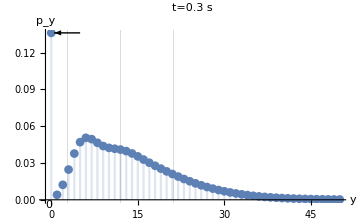
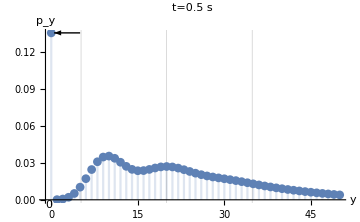

```mathematica
plots=Table[Show[DiscretePlot[SeriesCoefficient[g[1,s,t*0.1],{s,0,k}],{k,0,nmax},GridLines->{{{mean[t*0.1],Thick},{mean[t*0.1]-stddev[0.1 t],{Thick,Dashed}},{mean[t*0.1]+stddev[0.1 t],{Thick,Dashed}}},None},AxesLabel->{"y","p_y"},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},PlotLabel->"t="<>ToString[NumberForm[t*0.1,{2,1}]]<>" s",AxesOrigin->{origin,0},PlotMarkers->Automatic,Epilog->{Text[0,{origin,0},{origin,1.2}]}],Graphics[Arrow[{{5,g[1,0,t*0.1]},{0.5,g[1,0,t*0.1]}}]]],{t,{1,3,5}}]
```

```mathematica
Export[NotebookDirectory[]<>"../bilder/catalysis_mx=2_ktl=20_my0=0_t=0,1.pdf",plots[[1]]]
```

/home/matze/Paper/code/../bilder/catalysis_mx=2_ktl=20_my0=0_t=0,1.pdf

```mathematica
Export[NotebookDirectory[]<>"../bilder/catalysis_mx=2_ktl=20_my0=0_t=0,3.pdf",plots[[2]]]
```

/home/matze/Paper/code/../bilder/catalysis_mx=2_ktl=20_my0=0_t=0,3.pdf

```mathematica
Export[NotebookDirectory[]<>"../bilder/catalysis_mx=2_ktl=20_my0=0_t=0,5.pdf",plots[[3]]]
```

/home/matze/Paper/code/../bilder/catalysis_mx=2_ktl=20_my0=0_t=0,5.pdf

```mathematica
Table[DiscretePlot3D[SeriesCoefficient[g[sX,sY,t*0.1],{sX,0,kX},{sY,0,kY}],{kX,0,5},{kY,0,nmax},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14},AxesLabel->{"x","y","p_(x, y)"},ExtentSize->Full,PlotLabel->"t="<>ToString[NumberForm[t*0.1,{2,1}]]<>" s"],{t,{1,3,5}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
tab=Table[SeriesCoefficient[g[sX,sY,0.1],{sX,0,kX},{sY,0,kY}],{kX,0,5},{kY,0,nmax}];
```

```mathematica
Export[NotebookDirectory[]<>"/example1_t=0.1.csv",N[tab]]
```

/home/matze/Paper/code//example1_t=0.1.csv

```mathematica
tab2=Table[SeriesCoefficient[g[sX,sY,0.3],{sX,0,kX},{sY,0,kY}],{kX,0,5},{kY,0,nmax}];
```

```mathematica
Export[NotebookDirectory[]<>"/example1_t=0.3.csv",N[tab2]]
```

/home/matze/Paper/code//example1_t=0.3.csv

```mathematica
tab3=Table[SeriesCoefficient[g[sX,sY,0.5],{sX,0,kX},{sY,0,kY}],{kX,0,5},{kY,0,nmax}];
```

```mathematica
Export[NotebookDirectory[]<>"/example1_t=0.5.csv",N[tab3]]
```

/home/matze/Paper/code//example1_t=0.5.csv